```mathematica
K1=Import["D:\\Young_Lee_Current\\ZXH_PD\\R-strike\\old\\Z1.csv"];
```

```mathematica
K3=Import["D:\\Young_Lee_Current\\ZXH_PD\\R-strike\\old\\Z2.csv"];
```

```mathematica
A=ListPlot3D[K1,PlotStyle->Yellow]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\Ted\\Desktop\\L1.obj",A,"OBJ"]
```

C:\Users\Ted\Desktop\L1.obj

```mathematica
Export["C:\\Users\\Ted\\Desktop\\L1.3ds",A,"3DS"]
```

C:\Users\Ted\Desktop\L1.3ds

```mathematica
B=ListPlot3D[K3,PlotStyle->Green]
```

-Graphics3D-

```mathematica
Show[A,B]
```

-Graphics3D-

```mathematica
Show[%93,Background->LightGray]
```

-Graphics3D-

```mathematica
A1=ListPointPlot3D[K1,PlotStyle->Red ];
```

```mathematica
B1=ListPointPlot3D[K3,PlotStyle->Blue ];
```

```mathematica
Show[A1,B1]
```

-Graphics3D-

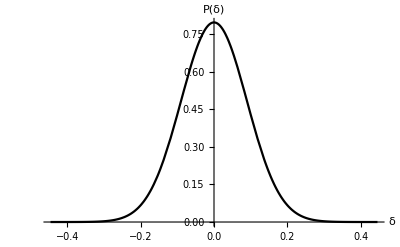

```mathematica
A=Plot[0.18PDF[NormalDistribution[0,0.09],x],{x,2*Log[0.8],-2*Log[0.8]},AxesLabel->{δ,P[δ]},PlotStyle->Black,AxesStyle->Directive[Orange, 12]]
```

```mathematica
Export["D:\\Young_Lee_Current\\ZXH_PD\\R-strike\\GS\\L1.svg",A,ImageSize-> {500*2,300*2}]
```

D:\Young_Lee_Current\ZXH_PD\R-strike\GS\L1.svg